```mathematica
Stability Analysis of Compartmental Model (Chapter 4)
```

```mathematica
Jacobian Matrix & Equilibrium Solutions
```

```mathematica
FullSimplify[Solve[{a*s*(1 - s) -s*(β01*i1 + β02*i2)==0,
 β01*s* i1+i1*i2*(β21 - β12) -ν1*i1==0, 
β02*s* i2 +i1*i2*(β12 - β21)- ν2*i2==0},{s,i1,i2}]]
```

{{s→1,i1→0,i2→0},{s→ν2/β02,i1→0,i2→(a (β02-ν2))/β02^2},{s→ν1/β01,i1→(a (β01-ν1))/β01^2,i2→0},{s→0,i1→ν2/(β12-β21),i2→-ν1/(β12-β21)},{s→0,i1→0,i2→0},{s→(a β12-a β21+β02 ν1-β01 ν2)/(a β12-a β21),i1→(-a (β12-β21) (β02-ν2)+β02 (-β02 ν1+β01 ν2))/(a (β12-β21)^2),i2→(a (β12-β21) (β01-ν1)+β01 (β02 ν1-β01 ν2))/(a (β12-β21)^2)}}

```mathematica
f= a*s*(1 - s) -s*(β01*i1 + β02*i2)
g = β01*s* i1+i1*i2*(β21 - β12) -ν1*i1
h =β02*s* i2 +i1*i2*(β12 - β21)- ν2*i2
```

a (1-s) s-s (i1 β01+i2 β02)

i1 s β01+i1 i2 (-β12+β21)-i1 ν1

i2 s β02+i1 i2 (β12-β21)-i2 ν2

```mathematica
FullSimplify[D[{f,g, h},{{s, i1, i2}}]]//MatrixForm
```

(a-2 a s-i1 β01-i2 β02 | -s β01 | -s β02
i1 β01 | s β01+i2 (-β12+β21)-ν1 | i1 (-β12+β21)
i2 β02 | i2 (β12-β21) | s β02+i1 (β12-β21)-ν2)

```mathematica
jacobian[s_, i1_, i2_]:=({{a-2 a s-i1 β01-i2 β02, -s β01, -s β02}, {i1 β01, s β01+i2 (-β12+β21)-ν1, i1 (-β12+β21)}, {i2 β02, i2 (β12-β21), s β02+i1 (β12-β21)-ν2}})
```

```mathematica
Disease-Free Equilibrium Eigenvalues
```

```mathematica
Eigenvalues[jacobian[1,0,0]] // FullSimplify
```

{-a,β01-ν1,β02-ν2}

```mathematica
Strain 1 Equilibrium Eigenvalues
```

```mathematica
Eigenvalues[jacobian[ν1/β01,(a (β01-ν1))/β01^2,0]] // FullSimplify
```

{-(a ν1+√a √ν1 √(a ν1+4 β01 (-β01+ν1)))/(2 β01),(-a ν1+√a √ν1 √(a ν1+4 β01 (-β01+ν1)))/(2 β01),(a (β12-β21) (β01-ν1)+β01 (β02 ν1-β01 ν2))/β01^2}

```mathematica
Strain 2 Equilibrium Eigenvalues
```

```mathematica
Eigenvalues[jacobian[ν2/β02,0,(a (β02-ν2))/β02^2]] // FullSimplify
```

{(-a (β12-β21) (β02-ν2)+β02 (-β02 ν1+β01 ν2))/β02^2,-(a ν2+√a √ν2 √(a ν2+4 β02 (-β02+ν2)))/(2 β02),(-a ν2+√a √ν2 √(a ν2+4 β02 (-β02+ν2)))/(2 β02)}

```mathematica
Strain Coexistence Equilibrium Eigenvalues
```

```mathematica
jacobian[(a β12-a β21+β02 ν1-β01 ν2)/(a β12-a β21),(-a (β12-β21) (β02-ν2)+β02 (-β02 ν1+β01 ν2))/(a (β12-β21)^2),(a (β12-β21) (β01-ν1)+β01 (β02 ν1-β01 ν2))/(a (β12-β21)^2)] // FullSimplify
```

{{(a (-β12+β21)-β02 ν1+β01 ν2)/(β12-β21),(β01 (a (-β12+β21)-β02 ν1+β01 ν2))/(a (β12-β21)),(β02 (a (-β12+β21)-β02 ν1+β01 ν2))/(a (β12-β21))},{(β01 (-a (β12-β21) (β02-ν2)+β02 (-β02 ν1+β01 ν2)))/(a (β12-β21)^2),0,β02-ν2+(β02 (β02 ν1-β01 ν2))/(a (β12-β21))},{(β02 (a (β12-β21) (β01-ν1)+β01 (β02 ν1-β01 ν2)))/(a (β12-β21)^2),β01-ν1+(β01 (β02 ν1-β01 ν2))/(a (β12-β21)),0}}

```mathematica
stabilityMatrix[a_, β01_, β02_, β12_, β21_, ν1_,ν2_ ]:= {{(a (-β12+β21)-β02 ν1+β01 ν2)/(β12-β21),(β01 (a (-β12+β21)-β02 ν1+β01 ν2))/(a (β12-β21)),(β02 (a (-β12+β21)-β02 ν1+β01 ν2))/(a (β12-β21))},{(β01 (-a (β12-β21) (β02-ν2)+β02 (-β02 ν1+β01 ν2)))/(a (β12-β21)^2),0,β02-ν2+(β02 (β02 ν1-β01 ν2))/(a (β12-β21))},{(β02 (a (β12-β21) (β01-ν1)+β01 (β02 ν1-β01 ν2)))/(a (β12-β21)^2),β01-ν1+(β01 (β02 ν1-β01 ν2))/(a (β12-β21)),0}}
```

```mathematica
eigenvals[a_, β01_, β02_, β12_, β21_, ν1_,ν2_ ] := AllTrue[Re[Eigenvalues[stabilityMatrix[a, β01, β02, β12, β21, ν1,ν2 ]]],TrueQ[#<0]&]
```

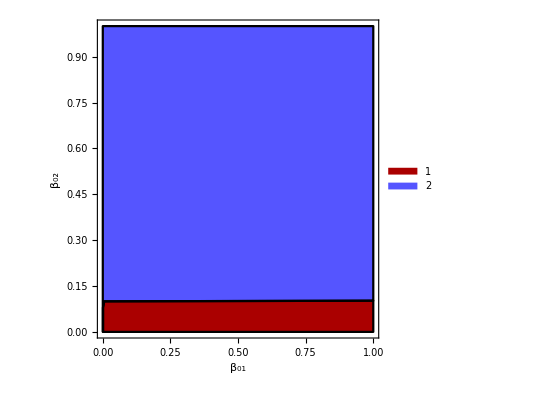

```mathematica
p1 = RegionPlot[{eigenvals[5000,β01, β02, 0.003, 0.002, 0.001,0.1], Not[eigenvals[5000,β01, β02, 0.003, 0.002, 0.001,0.1]]},{β01,0.0001,1},{β02,0.0001,1}, FrameLabel->{"β_01", "β_02"}, PlotStyle->{Darker[Red], Lighter[Blue]}, BoundaryStyle->Directive[Black, Thick], PlotLegends->Automatic]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

General::stop: Further output of Eigenvalues::inf will be suppressed during this calculation.

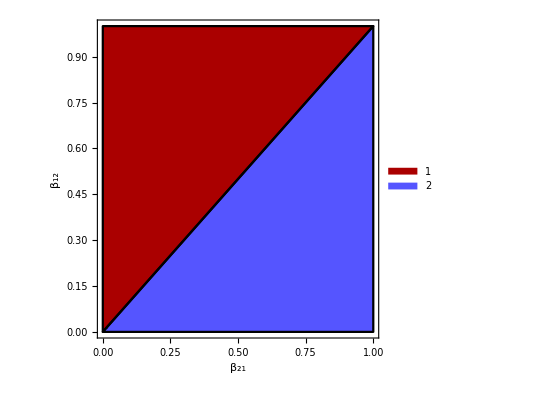

```mathematica
p2 =RegionPlot[{eigenvals[5000,0.78*1610.488/10000, 0.198*58.068/10000, β12,β21, 200/10000,1000/10000], Not[eigenvals[5000,0.78*1610.488/10000, 0.198*58.068/10000, β12,β21, 200/10000,1000/10000]]},{β21,0.0001,1},{β12,0.0001,1}, FrameLabel->{"β_21", "β_12"}, PlotStyle->{Darker[Red], Lighter[Blue]}, BoundaryStyle->Directive[Black, Thick], PlotLegends->Automatic]
```

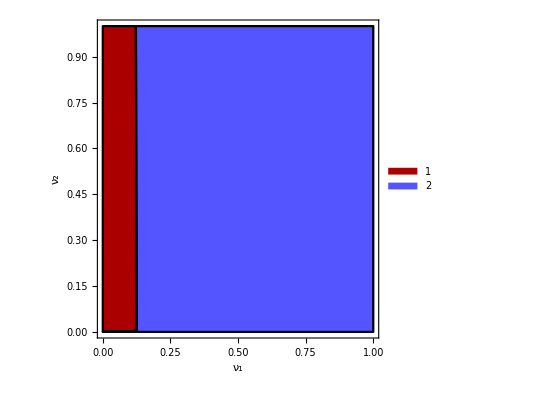

```mathematica
p3 =RegionPlot[{eigenvals[5000,0.78*1610.488/10000, 0.198*58.068/10000, 0.647*58.068/10000, 0.017*1610.488/10000, v1,v2], Not[eigenvals[5000,0.78*1610.488/10000, 0.198*58.068/10000, 0.647*58.068/10000, 0.017*1610.488/10000, v1,v2]]},{v1,0.0001,1},{v2,0.0001,1}, FrameLabel->{"ν_1", "ν_2"}, PlotStyle->{Darker[Red], Lighter[Blue]}, BoundaryStyle->Directive[Black, Thick], PlotLegends->Automatic]
```

```mathematica
plots = GraphicsGrid[{{p1,p2, p3}}, Epilog->{Inset[Style["A",15],Scaled[{-0.19,0.8}]],Inset[Style["B",15],Scaled[{0.31,0.8}]], Inset[Style["C",15],Scaled[{0.8,0.8}]]}]
```